```mathematica
NewtonRaphson[p0_,cifras_]:=Method[{},a=N[p0];e=10^(-N[cifras]);n=0;
b=a-N[f[a]/f'[a]];error=Abs[(b-a)/b];vector={{n,a,b,f[b],error}};
While[(((f(b)>e)||(error≥ 5*e))&&n≤20),a=b;b=a-f[a]/f'[a];error=Abs[(b-a)/b];n=n+1; vector=Append[vector,{n,a,b,f[b],error}]
];Print[NumberForm[TableForm[vector,TableHeadings->{None, {"n","p{n-1}","p{n}","f(p{n})","e_r"}}],16]];];
```

```mathematica
f[x_]:=E^(1-x/3)*x/3-0.25;
f'[x]
```

1/3 ⅇ^(1-x/3)-1/9 ⅇ^(1-x/3) x

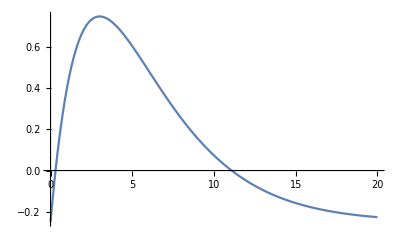

```mathematica
Plot[f[x],{x,0,20}]
```

```mathematica
NewtonRaphson[11,5]
```

n | p{n-1} | p{n} | f(p{n}) | e_r
0 | 11. | 11.07727359823909 | 0.00003828433225211425 | 0.006975867983560127
1 | 11.07727359823909 | 11.07790354509074 | 2.526545195280505×10^-9 | 0.00005686516849362809
2 | 11.07790354509074 | 11.07790358666909 | 5.551115123125783×10^-17 | 3.753268617160091×10^-9

Method[{},Null]

```mathematica
f[x_]:=(x+√x)(20-x+√(20-x))-155.5;
f'[x]
```

```mathematica
(1+1/(2 √x)) (20+√(20-x)-x)+(-1-1/(2 √(20-x))) (√x+x)
```

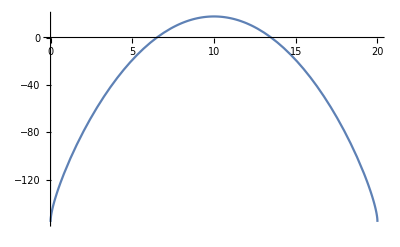

```mathematica
Plot[f[x],{x,0,20}]
```

```mathematica
NewtonRaphson[7,5]
```

n | p{n-1} | p{n} | f(p{n}) | e_r
0 | 7. | 6.466570501168851 | -0.4263187251486613 | 0.0824903244671546
1 | 6.466570501168851 | 6.507711123715651 | -0.002559321802408476 | 0.006321826793582332
2 | 6.507711123715651 | 6.507961104282696 | -9.44162081850664×10^-8 | 0.00003841150293307683

Method[{},Null]

```mathematica
NewtonRaphson[13,5]
```

n | p{n-1} | p{n} | f(p{n}) | e_r
0 | 13. | 13.53342949883115 | -0.4263187251486613 | 0.03941569273902228
1 | 13.53342949883115 | 13.49228887628435 | -0.002559321802408476 | 0.00304919520505627
2 | 13.49228887628435 | 13.4920388957173 | -9.44161513416475×10^-8 | 0.00001852800521689444

Method[{},Null]

```mathematica
Secante[x0_,x1_,cifras_]:=
Module[{},a=N[x0];b=N[x1];e=10^(-N[cifras]);n=1;
error=(b-a)/b;vector={{n,a,b,f[b],error}};
While[Abs[f[b]]>e&&Abs[error]>5*e&&n≤40,
c=(b*f[a]-a*f[b])/(f[a]-f[b]);a=b;
b=c;
error=(b-a)/b;
n=n+1;
vector=Append[vector,{n,a,b,f[b],error}];

];
Print[NumberForm[TableForm[vector,TableHeadings->{None, {"n","x(n-1)","xn","f(xn)","er"}}],16]];
];
```

```mathematica
f[x_]=0.6546 x(1-E^(-150/x))-36;
```

```mathematica
Secante[58.5,61.5,4]
```

n | x(n-1) | xn | f(xn) | er
1 | 58.5 | 61.5 | 0.7455621578666083 | 0.04878048780487805
2 | 61.5 | 59.90197598894598 | 0.006271058105077998 | -0.02667731714474505
3 | 59.90197598894598 | 59.88842070411993 | -0.00006091241168348915 | -0.0002263423324021966

```mathematica
f[x_]:= 0.6546 x(1-E^(-150/x))-36;
```

```mathematica
NewtonRaphson[59.9,4]
```

n | p{n-1} | p{n} | f(p{n}) | e_r
0 | 59.9 | 59.88855030698891 | -3.67198296657989×10^-7 | 0.0001911833389252065

Method[{},Null]

```mathematica
NewtonRaphson[58.5,4]
```

n | p{n-1} | p{n} | f(p{n}) | e_r
0 | 58.5 | 59.87709614034614 | -0.005351653490379249 | 0.02299871284870528
1 | 59.87709614034614 | 59.88855030627528 | -3.675316833096076×10^-7 | 0.0001912580262932917

Method[{},Null]

```mathematica
New
```

New

```mathematica
NewtonRaphson[95,4]
```

n | p{n-1} | p{n} | f(p{n}) | e_r
0 | 95. | 51.39785150960226 | -4.172454768443959 | 0.848326286211631
1 | 51.39785150960226 | 59.48337071589148 | -0.1897441023365474 | 0.1359290690655011
2 | 59.48337071589148 | 59.88756929063387 | -0.000458660662346233 | 0.006749290036815748
3 | 59.88756929063387 | 59.88855108723302 | -2.700133450161957×10^-9 | 0.00001639372770450876

Method[{},Null]